Calcolo della FdT per un sistema LTI-TC. Immetto i parametri del sistema (A, B, C, D)

```mathematica
A=({{0, 1, 0}, {0, 0, 1}, {-10, -17, -8}});B=({{0}, {0}, {1}});Cc=({{1, -1, 0}});
```

L’espressione della FdT, una volta assegnata la rappresentazione ISU e’

```mathematica
G[s_]:=Simplify[Cc.Inverse[s IdentityMatrix[3]-A].B][[1,1]]
```

```mathematica
G[s]
```

(1-s)/(10+17 s+8 s^2+s^3)

Fatto: la FdT per un sistema LTI-TC e’ una frazione algebrica in s 

in cui il grado del denominatore non eccede quello del denominatore.
Il tutto si basa sull’analisi del calcolo della matrice aggiogata (o aggiunta) di s I - A

```mathematica
Adjugate[s IdentityMatrix[3]-A]//MatrixForm
```

(17+8 s+s^2 | 8+s | 1
-10 | 8 s+s^2 | s
-10 s | -10-17 s | s^2)

In questo caso ho una tabella di polinomi che al massimo hanno grado pari a 2 (la matrice aggiogata si ottiene giustapponendo minori di ordine n-1, se n = 3 il minore ha ordine 2 da cui il polinomio di secondo grado).
Determino ora i poli del sistema

```mathematica
Solve[Denominator[G[s]]==0,s]
```

{{s→-5},{s→-2},{s→-1}}

```mathematica
Eigenvalues[A]
```

{-5,-2,-1}

Mi calcolo gli zeri del sistema che sono le radici del numeratore della funzione di trasferimento

```mathematica
Solve[Numerator[G[s]]==0,s]
```

{{s→1}}

Mi calcolo la risposta forzata al gradino unitario, tenendo conto che essa e’ il prodotto algebrico fra la FdT del sistema e la L-trasformata dell’ingresso

```mathematica
LaplaceTransform[UnitStep[t],t,s]
```

1/s

La risposta forzata, nel caso nostro e’

```mathematica
G[s]/s
```

(1-s)/(s (10+17 s+8 s^2+s^3))

```mathematica
Apart[G[s]/s,s]
```

1/(10 s)-1/(2 (1+s))+1/(2 (2+s))-1/(10 (5+s))

La risposta forzata in s e’ la somma di quattro fratti semplici

```mathematica
Subscript[Y, f][s_]:=Subscript[C, 1]/s+Subscript[C, 2]/(s+1)+Subscript[C, 3]/(s+2)+Subscript[C, 4]/(s+5)
```

Applico la Formula semplificata di Heaviside per calcolarmi i coefficienti

```mathematica
Subscript[C, 1]=lim_(s->0) s G[s]/s
```

1/10

```mathematica
Subscript[C, 2]=lim_(s->-1) (s+1) G[s]/s
```

-1/2

```mathematica
Subscript[C, 3]=lim_(s->-2) (s+2) G[s]/s
```

1/2

```mathematica
Subscript[C, 4]=lim_(s->-5) (s+5) G[s]/s
```

-1/10

```mathematica
Subscript[Y, f][s]
```

1/(10 s)-1/(2 (1+s))+1/(2 (2+s))-1/(10 (5+s))

```mathematica
Subscript[y, f][t_]:=InverseLaplaceTransform[Subscript[Y, f][s],s,t]
```

```mathematica
Subscript[y, f][t]
```

1/10 ⅇ^(-5 t) (-1+5 ⅇ^(3 t)-5 ⅇ^(4 t)+ⅇ^(5 t))

```mathematica
Expand[Subscript[y, f][t]]
```

1/10-ⅇ^(-5 t)/10+ⅇ^(-2 t)/2-ⅇ^-t/2

```mathematica
Expand[InverseLaplaceTransform[G[s]/s,s,t]]
```

1/10-ⅇ^(-5 t)/10+ⅇ^(-2 t)/2-ⅇ^-t/2

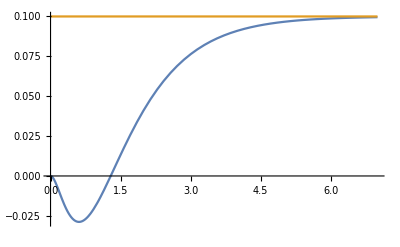

```mathematica
Plot[{Subscript[y, f][t],Subscript[C, 1] UnitStep[t]},{t,0,7}]
```

```mathematica
LaplaceTransform[Sin[t]UnitStep[t],t,s]
```

1/(1+s^2)

Mi calcolo la risposta forzata al segnale periodico elementare sin( t ) 1(t)

```mathematica
G[s]LaplaceTransform[Sin[t],t,s]
```

(1-s)/((1+s^2) (10+17 s+8 s^2+s^3))

```mathematica
Apart[G[s]LaplaceTransform[Sin[t],t,s],s]
```

1/(4 (1+s))-1/(5 (2+s))+1/(52 (5+s))+(-7-9 s)/(130 (1+s^2))